```mathematica
Quit[]
```

```mathematica
Print["Gussian Filter: ", Checkbox[Dynamic[GsF]]]
```

Gussian Filter:

```mathematica
SetDirectory[NotebookDirectory[]];
dataRF= Import[".\\rf.dat","Table"];
Print["File loaded."]
(*dataRF=dataRF/1000;*)
For[i=1,i<Length[dataRF]+1, 
	For[j=1,j<4,
{dataRF[[i,j]]=dataRF[[i,j]]/1000}
j++];
i++]

(*Gussian Filters*)
(*RF1F=Table[0x y,{x,Length[dataRF1]},{y,4}];
RF1G=GaussianFilter[Table[dataRF1[[i,4]],{i,1,Length[dataRF1]}],{2,2}];
For[i=1,i<Length[RF1G]+1,i++,
{RF1F[[i,3]]=dataRF[[i,3]];
RF1F[[i,2]]=dataRF[[i,2]];
RF1F[[i,1]]=dataRF[[i,1]];
RF1F[[i,4]]=RF1G[[i]];
}];

RF1F=Table[0x y,{x,Length[dataRF1]},{y,4}];
RF1G=GaussianFilter[Table[dataRF1[[i,4]],{i,1,Length[dataRF1]}],{2,2}];
For[i=1,i<Length[RF1G]+1,i++,
{RF1F[[i,3]]=dataRF1[[i,3]];
RF1F[[i,2]]=dataRF1[[i,2]];
RF1F[[i,1]]=dataRF1[[i,1]];
RF1F[[i,4]]=RF1G[[i]];
}];

RF2F=Table[0x y,{x,Length[dataRF2]},{y,4}];
RF2G=GaussianFilter[Table[dataRF2[[i,4]],{i,1,Length[dataRF2]}],{2,2}];
For[i=1,i<Length[RF2G]+1,i++,
{RF2F[[i,3]]=dataRF2[[i,3]];
RF2F[[i,2]]=dataRF2[[i,2]];
RF2F[[i,1]]=dataRF2[[i,1]];
RF2F[[i,4]]=RF2G[[i]];
}];

RF3F=Table[0x y,{x,Length[dataRF3]},{y,4}];
RF3G=GaussianFilter[Table[dataRF3[[i,4]],{i,1,Length[dataRF3]}],{2,2}];
For[i=1,i<Length[RF3G]+1,i++,
{RF3F[[i,3]]=dataRF3[[i,3]];
RF3F[[i,2]]=dataRF3[[i,2]];
RF3F[[i,1]]=dataRF3[[i,1]];
RF3F[[i,4]]=RF3G[[i]];
}];

RF4F=Table[0x y,{x,Length[dataRF4]},{y,4}];
RF4G=GaussianFilter[Table[dataRF4[[i,4]],{i,1,Length[dataRF4]}],{2,2}];
For[i=1,i<Length[RF4G]+1,i++,
{RF4F[[i,3]]=dataRF4[[i,3]];
RF4F[[i,2]]=dataRF4[[i,2]];
RF4F[[i,1]]=dataRF4[[i,1]];
RF4F[[i,4]]=RF4G[[i]];
}];
Print["Gussian filter applied."])*)

RF1F = Interpolation[dataRF,InterpolationOrder->4]
Off[FindMinimum::lstol]
Off[FindMaximum::lstol]
Off[InterpolatingFunction::dmval]
```

File loaded.

InterpolatingFunction[{{-0.0005,0.0005},{-0.0005,0.0005},{0.,0.0005}},<>]

```mathematica
(*BOUNDARY of plot*)
xkoord1=-0.0005;
xkoord2=-xkoord1;
ykoord1=-0.0005;
ykoord2=-xkoord1;
zkoord1=0.000;
zkoord2=0.00030;
rfBrXend=-0.0005;
rfBrXEnd=0.0;
rfBrZend=0.00003;
rfBrZEnd=0.0003;
LNx=-0.0005;
rfBrPts=60;

RFblubb[x_,y_,z_]:=(RF1F[x ,y ,z]);

(*q is set to 0.20 and trapdepth = 0.1 eV*)
```

-Graphics3D-

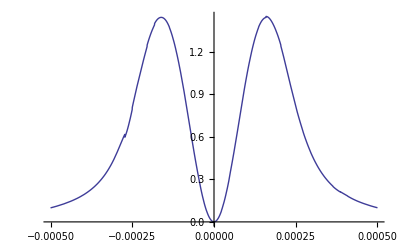

This is the potential - z

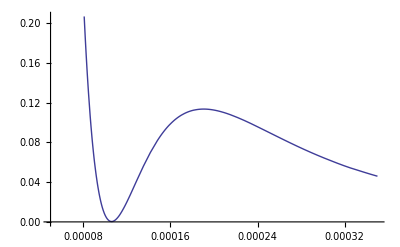

The actual ion height is 105.824 um

Escaping position is 201.066 um

The secular frequency is {2.06726×10^6,2.04004×10^6}

The Q parameter along x is 0.194903

Trap depth (in eV) is 0.11193

The rotation (in degree) is -84.3184.

Normalized Inhomogenous factor is 1.77832

Homogenously mapped Q parameter is 0.346601

RF driving source is 250V, 60 πMHz

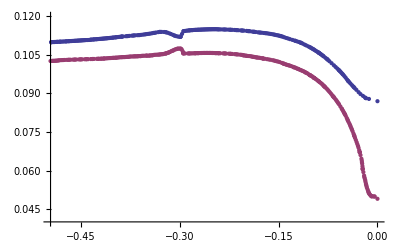

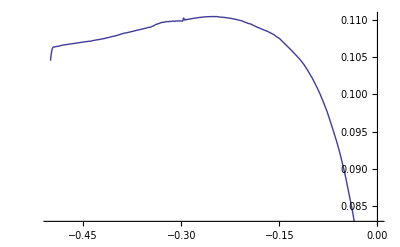

Contour plot

-Graphics-

Change of rf barrier

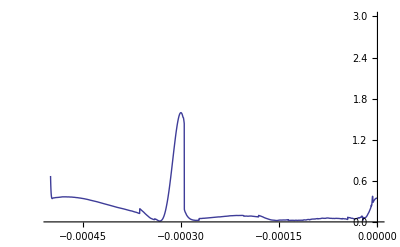

The max of barrier is 0.365826%

```mathematica
RFbase[x_,y_,z_] =Vrf*RFblubb[x,y,z];
pondpotential[x_,y_,z_] = ((D[RFbase[x,y,z],x])^2 + (D[RFbase[x,y,z],y])^2+ (D[RFbase[x,y,z],z])^2);
TotalPotentialNum[x_,y_,z_] = ψ pondpotential[x,y,z];
DeriveTPXNum[x_,y_,z_]=D[TotalPotentialNum[x,y,z],x];
DeriveTPYNum[x_,y_,z_]=D[TotalPotentialNum[x,y,z],y];
DeriveTPZNum[x_,y_,z_]=D[TotalPotentialNum[x,y,z],z];



NumMinArr=FindMinimum[{TotalPotentialNum[LNx,0,z]},{z,AimedIonHeight},Method->"Newton"];
IonHeightActual=z/.NumMinArr[[2]];
xRootNum=x/.FindRoot[{DeriveTPXNum[x,y,z]==0,DeriveTPZNum[x,y,z]==0,DeriveTPYNum[x,y,z]==0},{{y,0},{x,LNx},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
yRootNum=y/.FindRoot[{DeriveTPXNum[x,y,z]==0,DeriveTPZNum[x,y,z]==0,DeriveTPYNum[x,y,z]==0},{{x,LNx},{y,0},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
zRootNum=z/.FindRoot[{DeriveTPXNum[x,y,z]==0,DeriveTPZNum[x,y,z]==0,DeriveTPYNum[x,y,z]==0},{{x,LNx},{y,0},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
HessNumMat[x_,y_,z_]=D[TotalPotentialNum[x,y,z],{{x,y,z},2}];
EigenvaluesNum=Take[Eigenvalues[HessNumMat[LNx,0,zRootNum]],2];
SecFreqNum=Sqrt[EigenvaluesNum/mYb]/(2π);
NumMaxArr=FindMaximum[{TotalPotentialNum[LNx,0,z],2*IonHeightActual>z>IonHeightActual},{z,zEscape}];
NumMax=z/.NumMaxArr[[2]];
Plot3D[TotalPotentialNum[x,y,IonHeightActual]/e,{x,xkoord1,xkoord2},{y,ykoord1,ykoord2},ColorFunction->Hue,AspectRatio->Automatic]
Plot[TotalPotentialNum[LNx,y,IonHeightActual]/e,{y,ykoord1,ykoord2}]
Print["This is the potential - z"]
Plot[TotalPotentialNum[LNx,0,test]/e,{test,0.00005,0.00035}]
Print["The actual ion height is ", 1000*1000*IonHeightActual," um"]
Print["Escaping position is ",1000*1000*NumMax," um"]
Print["The secular frequency is ", SecFreqNum]
Qpara=N[2Sqrt[2]*2π*SecFreqNum[[1]]/Ω,3];
Print["The Q parameter along x is ", Qpara]
TrapDepthNum=(TotalPotentialNum[LNx,0,NumMax]-TotalPotentialNum[LNx,0,IonHeightActual])/e;
Print["Trap depth (in eV) is ",TrapDepthNum ]
EVecNum=Eigenvectors[HessNumMat[xRootNum,yRootNum,IonHeightActual]];
Print["The rotation (in degree) is ", -90+(180/π)* ArcCos[EVecNum[[1,3]]],". "]

DrevRF1Num[x_,y_,z_]=D[RFbase[x,y,z],x]+D[RFbase[x,y,z],y]+D[RFbase[x,y,z],z];

InhomoNum[x_,y_,z_]=(2e)/(mYb Ω^2)(Abs[D[DrevRF1Num[x,y,z],x]]+Abs[D[DrevRF1Num[x,y,z],y]]+Abs[D[DrevRF1Num[x,y,z],z]]);


zInhomoNum=z/.FindRoot[TotalPotentialNum[LNx,0,z]-TotalPotentialNum[LNx,0,NumMax]==0,{z,IonHeightActual-0.00005}];

InhomoThetaNum=InhomoNum[LNx,0,zInhomoNum]/InhomoNum[LNx,0,IonHeightActual];

Print["Normalized Inhomogenous factor is ",InhomoThetaNum]
Print["Homogenously mapped Q parameter is ", InhomoThetaNum*Qpara]
Print["RF driving source is " ,Vrf,"V, ", Ω*10^-6, "MHz"]

(*====RF Barrier部分====*)

rfBrTab=Cases[Normal@ContourPlot[TotalPotentialNum[x/1000,0 ,z/1000 ]/e,{x,rfBrXend*1000,-0.00000*1000},{z,0.00002*1000,0.00026*1000},Contours->{0.002400}],Line[pts_]->pts,Infinity];
rfBrTab[[1]]=MovingMedian[rfBrTab[[1]],6];
rfBrTab[[2]]=MovingMedian[rfBrTab[[2]],6];
rfBrTab[[2]]=Insert[rfBrTab[[2]],{-0.0,0.049},1];
rfBrTab[[1]]=Insert[rfBrTab[[1]],{-0.0,0.087},1];
ListPlot[rfBrTab,PlotRange->{Automatic,{0.04,0.12}}]
p1=Interpolation[rfBrTab[[1]]];
p2=Interpolation[rfBrTab[[2]]];
Clear[rfBrIP]
rfBrIP[x_]:=(p1[x]+p2[x])/2
(*fline=Interpolation[Table[{x,0.0883-0.01 x} ,{x,-0.007,0,0.0001}]];
rfBrIP[x_]=Piecewise[{{fline[x],-0.025<x<0},{rfBrIP[x],-0.5<x<-0.025}}];*)
tmp2=Plot[{rfBrIP[x]},{x,0,-0.5}]
Print["Contour plot"]
tmp3=ContourPlot[TotalPotentialNum[x/1000,0 ,z/1000 ]/e,{x,rfBrXend*1000,0},{z,rfBrZend*1000,rfBrZEnd*1000},Contours->120,AspectRatio->Automatic,FrameLabel->{"x (mm)","y (mm)"}, ContourLabels->Automatic,ColorFunction->Hue,PlotRange->{Automatic,{0.00004*1000,0.00015*1000}},ImageSize->Full];
Show[tmp3,tmp2]
Print["Change of rf barrier"]
Plot[TotalPotentialNum[x,0,rfBrIP[x*1000]/1000]/(e)/TrapDepthNum*100,{x,rfBrXend,0},PlotRange->{Automatic,{0,3}}]
Print["The max of barrier is ", NMaxValue[{TotalPotentialNum[x,0,rfBrIP[x*1000]/1000]/e,-0.0005<=x<-0.00005},x]/TrapDepthNum*100,"%"]
```

```mathematica
ContourPlot[TotalPotentialNum[x/1000,0 ,z/1000 ]/e,{x,-rfBrXend*1000,0},{z,rfBrZend*1000,rfBrZEnd*1000},Contours->120,AspectRatio->Automatic,FrameLabel->{"x (mm)","y (mm)"}, ContourLabels->Automatic,ColorFunction->Hue,PlotRange->{Automatic,{0.00004*1000,0.00015*1000}},ImageSize->Full]
```

-Graphics-

```mathematica
Print["The max of barrier is ", NMaxValue[{TotalPotentialNum[x,0,rfBrIP[x*1000]/1000]/e,-0.0002<=x<-0.00005},x]/TrapDepthNum*100,"%"]
```

The max of barrier is 0.0855487%

```mathematica
ContourPlot[TotalPotentialNum[0,x/1000 ,z/1000 ]/e,{x,rfBrXend*1000,-rfBrXend*1000},{z,rfBrZend*1000,rfBrZEnd*1000},Contours->120,AspectRatio->Automatic,FrameLabel->{"x (mm)","y (mm)"}, ContourLabels->Automatic,ColorFunction->Hue,PlotRange->{Automatic,{0.00004*1000,0.00015*1000}},ImageSize->Full]
```

-Graphics-

The sharpe increase of rf barrier near the -0.3 mm does not happen on the other arm at 0.3 mm which means it is not real.